```mathematica
(*Some global parameters for plotting*)
myAxesSize=21;
myLabelSize=18;
myImageSize=1000;
SetDirectory[NotebookDirectory[]];
```

# P delta curve

### Parameters

```mathematica
Ela=30.;
ν=0.2;
G=1.2 10^-4;
l=10.;
L=200.;
```

### Sigma and u peak

```mathematica
sigpeak=√((27 Ela G)/(256 l))
upeak=16/9(sigpeak L)/Ela
```

0.00616188

0.0730297

### Reading solution and plotting

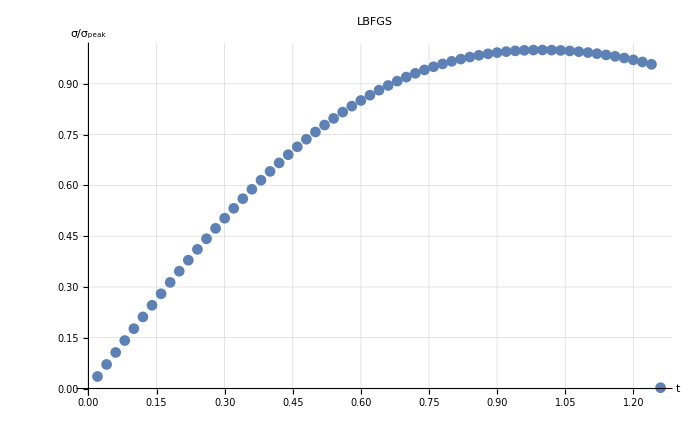

```mathematica
file=Import["build/pdelta_ex1.txt","Table"];
file[[;;,2]]/=sigpeak;
ListPlot[file,ImageSize->myImageSize 0.7,AxesLabel->{Style["t",myAxesSize,Black],Style["σ/σ_peak",myAxesSize,Black]},LabelStyle->Directive[myLabelSize*0.8,Bold,Black],GridLines->Automatic,PlotLabel->"LBFGS"]
```